```mathematica
ClearAll["Global'*"]
G[r1_,r2_]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G2[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G3[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G4[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
```

```mathematica
y0={100,100}
y0hat:=y0/Norm[y0];
epsilon=1/Norm[y0];
```

{100,100}

```mathematica
theta1[t_]=Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}];
```

```mathematica
theta2[t_]=Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}];
omega1[t_]=Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}];
omega2[t_]=Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}];
```

```mathematica
x1[t_]={Cos[theta1[t]],Sin[theta1[t]]};
x2[t_]={Cos[theta2[t]],Sin[theta2[t]]};
```

```mathematica
dx1[t_]={-omega1[t]Sin[theta1[t]],omega1[t]Cos[theta1[t]]};
```

```mathematica
dx2[t_]={-omega2[t]Sin[theta2[t]],omega2[t]Cos[theta2[t]]};
```

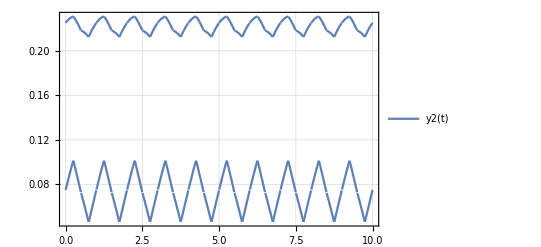

```mathematica
y2[t_]=G2[y0hat].x1[t]+ G2[y0hat].x2[t];
Plot[y2[t],{t,0,10},PlotTheme->"Detailed"]
```

```mathematica
y21[t_,a_,b_]:=G[a,b].(x1[t]+x2[t]);
y22=NDSolveValue[{y'[t]==(3/40)(y0hat.x1[t] dx1[t]+3 y0hat (y0hat.x1[t])(y0hat.dx1[t])+(y0hat.x2[t] )dx2[t]+3 y0hat (y0hat.x2[t])( y0hat.dx2[t]) - y0hat (x1[t].dx1[t])-y0hat (x2[t].dx2[t])-x1[t] (y0hat.dx1[t])-x2[t]( y0hat.dx2[t])),y[0]=={0,0}},y,{t,0,1},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->17];
y23=NDSolveValue[{y'[t]==(3/40)(y2[t] y0hat.dx1[t]+y2[t] y0hat.dx2[t]+y0hat y2[t].(dx1[t]+dx2[t])-(dx1[t]+dx2[t])(y0hat.y2[t])-3(y2[t].y0hat)(y0hat.(dx1[t]+dx2[t])y0hat)),y[0]=={0,0}},y,{t,0,1},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->17];
```

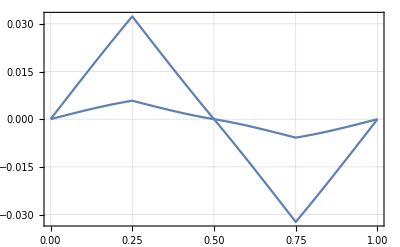

```mathematica
Plot[y22[t],{t,0,1},PlotTheme->"Detailed",PlotLegends->"y_{22}(t)"]
```

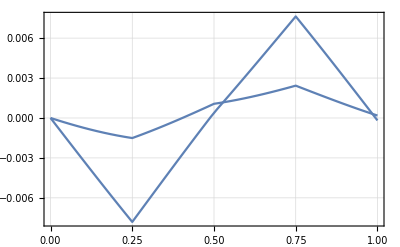

```mathematica
Plot[y23[t],{t,0,1},PlotTheme->"Detailed",PlotLegends->"y_{23}(t)"]
```

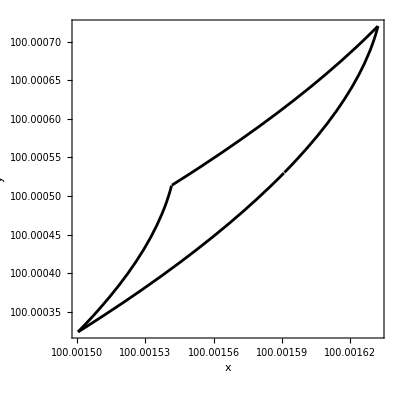

```mathematica
theta11[t_?NumericQ]=Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}];
theta21[t_?NumericQ]=Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}];
omega11[t_?NumericQ]=Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}];
omega21[t_?NumericQ]=Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}];
x11[t_?NumericQ]={Cos[theta1[t]],Sin[theta1[t]]};
x21[t_?NumericQ]={Cos[theta2[t]],Sin[theta2[t]]};
dx11[t_?NumericQ]={-omega1[t]Sin[theta1[t]],omega1[t]Cos[theta1[t]]};
dx21[t_?NumericQ]={-omega2[t]Sin[theta2[t]],omega2[t]Cos[theta2[t]]};

y3=NDSolveValue[{b'[t]==G2[b[t]-x11[t]].dx11[t]+G2[b[t]-x21[t]].dx21[t],b[0]==y0},b,{t,0,1},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->17];

curve=ParametricPlot[{y0+epsilon y2[t]+epsilon^2 y22[t]+epsilon^3 y23[t]},{t,0,1},AspectRatio->1, FrameLabel->{"x","y"},PlotTheme->"Scientific",PerformanceGoal->"Quality",PlotRange->Full,PlotStyle->{{Black, Thickness[0.005]},{Dashed, Black,Thickness[0.005]}}]
```

```mathematica
diff[a_,c_]=ParametricNDSolveValue[{b'[t]==G2[b[t]-x11[t]].dx11[t]+G2[b[t]-x21[t]].dx21[t],b[0]=={a,c}},b[1]-b[0],{t,0,1},{a,c},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->17];
```

```mathematica
diff2[a_,c_]=ParametricNDSolveValue[{b'[t]==(3/40)(y2[t] y0hat.dx1[t]+y2[t] y0hat.dx2[t]+y0hat y2[t].(dx1[t]+dx2[t])-(dx1[t]+dx2[t])(y0hat.y2[t])-3(y2[t].y0hat)(y0hat.(dx1[t]+dx2[t])y0hat)),b[0]=={a,c}},b[1]-b[0],{t,0,1},{a,c},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->17];
```

```mathematica
Integrate[(3/4)(y21[t,q,p] {q,p}.dx1[t]+y21[t,q,p] {q,p}.dx2[t]+{q,p} y21[t,q,p] .(dx1[t]+dx2[t])-(dx1[t]+dx2[t])({q,p}.y21[t,q,p] )-3(y21[t,q,p] .{q,p})({q,p}.(dx1[t]+dx2[t]){q,p})),{t,0,1}]
```

{(27 (2 p^3 Sin[1/4]+2 p q^2 Sin[1/4]-p^3 Sin[1/2]-p q^2 Sin[1/2]))/(160 (p^2+q^2)^(3/2)),-(27 (8 p^2 q^3 Cos[1/8]^3 Sin[1/8]+2 p^2 q Sin[1/4]+2 q^3 Sin[1/4]-2 p^2 q^3 Sin[1/4]-p^2 q Sin[1/2]-q^3 Sin[1/2]-p^2 q^3 Sin[1/2]))/(160 (p^2+q^2)^(3/2))}

```mathematica
Simplify[{(27 (2 p^3 Sin[1/4]+2 p q^2 Sin[1/4]-p^3 Sin[1/2]-p q^2 Sin[1/2]))/(160 (p^2+q^2)^(3/2)),-(27 (8 p^2 q^3 Cos[1/8]^3 Sin[1/8]+2 p^2 q Sin[1/4]+2 q^3 Sin[1/4]-2 p^2 q^3 Sin[1/4]-p^2 q Sin[1/2]-q^3 Sin[1/2]-p^2 q^3 Sin[1/2]))/(160 (p^2+q^2)^(3/2))}]
```

```mathematica
diff3[q_,p_]:={(27 p Cos[1/8] Sin[1/8]^3)/(20 √(p^2+q^2)),-(27 q Cos[1/8] Sin[1/8]^3)/(20 √(p^2+q^2))}
```

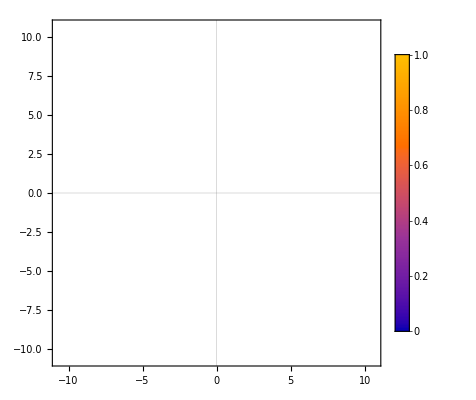

```mathematica
VectorPlot[diff3[{q,p}],{q,-10,10},{p,-10,10},PlotLegends->Automatic,PlotTheme->"Scientific"]
```